```mathematica
(* Define Arditi-Akcakaya model and true parameter/variable values *)
```

```mathematica
AA=a N / (P^(m+bias) + a h N)
TruePar={P-> 2, N->2,m->1,a -> 0.5, h-> 2};
TrueF = f1/.TruePar/.bias->0
```

(a N)/(a h N+P^(bias+m))

0.25

```mathematica
AAa[b_]=Solve[F==AA ,a][[1]][[1,2]]//Simplify
AAh[b_]=Solve[F==AA ,h][[1]][[1,2]]//Simplify
```

(F P^(bias+m))/(N-F h N)

1/F-P^(bias+m)/(a N)

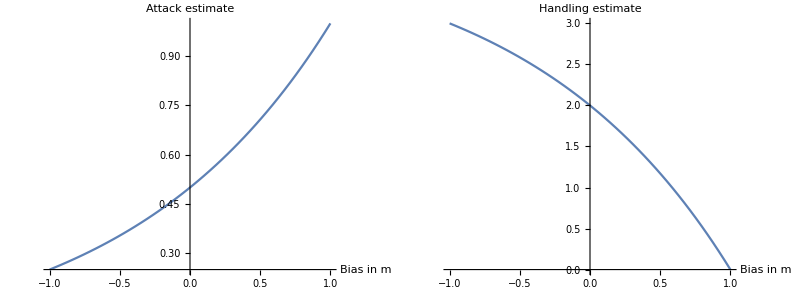

```mathematica
Grid[{{
Plot[AAa[b]/.F->TrueF/.Drop[TruePar,{4}],{bias,-1,1},AxesLabel->{"Bias in m","Attack estimate"}],
Plot[AAh[b]/.F->TrueF/.Drop[TruePar,{5}],{bias,-1,1},AxesLabel->{"Bias in m","Handling estimate"}]
}}]
```

```mathematica
Manipulate[
TruePar={P-> Π, N->Ν,m->μ,a -> α, h-> η};
TrueF = AA/.TruePar/.bias->0;

Grid[{{
Plot[AAa[b]/.F->TrueF/.Drop[TruePar,{4}],{bias,-1,1},AxesLabel->{"Bias in m","Attack estimate"}],
Plot[AAh[b]/.F->TrueF/.Drop[TruePar,{5}],{bias,-1,1},AxesLabel->{"Bias in m","Handling estimate"}]
}}],

{{Π,2,P},1,10},
{{Ν,5,N},1,10},
{{μ,1,m},0,2},
{{α,0.5,a},0,1},
{{η,2,h},0,3}
]
```

```mathematica
(* Define Beddington-DeAngelis model and true parameter/variable values *)
```

```mathematica
BD=a N / (1 + a h N + (c+bias)P)
TruePar={P-> 2, N->2,c->1,a -> 0.5, h-> 2};
TrueF = BD/.TruePar/.bias->0
```

(a N)/(1+a h N+(bias+c) P)

0.2

```mathematica
BDa[b_]=Solve[F==BD ,a][[1]][[1,2]]//Simplify
BDh[b_]=Solve[F==BD ,h][[1]][[1,2]]//Simplify
```

(F (1+bias P+c P))/(N-F h N)

(a N-F (1+bias P+c P))/(a F N)

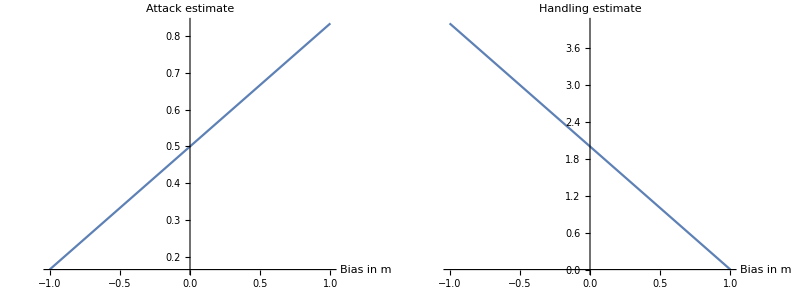

```mathematica
Grid[{{
Plot[BDa[b]/.F->TrueF/.Drop[TruePar,{4}],{bias,-1,1},AxesLabel->{"Bias in m","Attack estimate"}],
Plot[BDh[b]/.F->TrueF/.Drop[TruePar,{5}],{bias,-1,1},AxesLabel->{"Bias in m","Handling estimate"}]
}}]
```

```mathematica
Manipulate[
TruePar={P-> Π, N->Ν,c->χ,a -> α, h-> η};
TrueF = BD/.TruePar/.bias->0;

Grid[{{
Plot[BDa[b]/.F->TrueF/.Drop[TruePar,{4}],{bias,-1,1},AxesLabel->{"Bias in m","Attack estimate"}],
Plot[BDh[b]/.F->TrueF/.Drop[TruePar,{5}],{bias,-1,1},AxesLabel->{"Bias in m","Handling estimate"}]
}}],

{{Π,2,P},1,10},
{{Ν,5,N},1,10},
{{χ,1,c},0,2},
{{α,0.5,a},0,1},
{{η,2,h},0,3}
]
```